## Parámetros Comunes

```mathematica
ColoresTema=ColorData[106,"ColorList"];
```

## Modelo

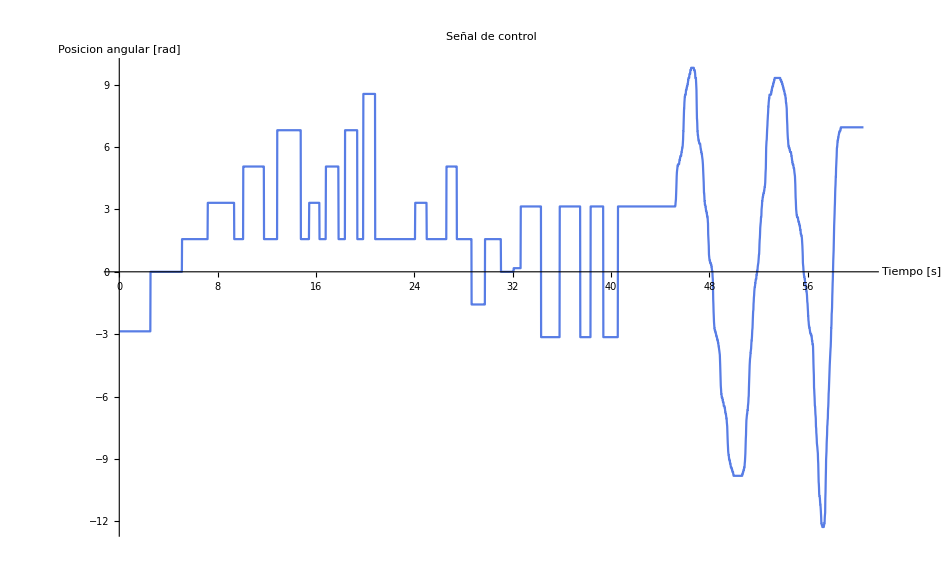

```mathematica
Ubicacion="C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\Genomas\\Validacion";
SetDirectory[Ubicacion];
SeñalControl=Import["ControlSignal.csv","Data"];
GSC=ListLinePlot[SeñalControl,
PlotLabel->"Señal de control",
AxesLabel->{"Tiempo [s]","Posicion angular [rad]"},
PlotStyle->ColoresTema[[1]]
]
τ=Median[Differences[SeñalControl[[;;,1]]]];
RespuestaMotor=Import["MotorReactionToControlP.csv","Data"];
ListLinePlot[RespuestaMotor];
Export["ControlSignal.eps",GSC];
```

```mathematica
kv=0.031;k=0.031; Ra=0.27; La=0.4 10^-3; d=1.21 10^-5; J=2.61 10^-5*9.81;
Eq1=kv ωp[t]==−Ra ia[t]−La ia'[t]+Vt[t]
Eq2=k ia[t]==J ωp'[t]+d ωp[t]
Eq3=D[Eq2,t]
```

0.031 ωp[t]==-0.27 ia[t]+Vt[t]-0.0004 ia'[t]

0.031 ia[t]==0.0000121 ωp[t]+0.000256041 ωp'[t]

0.031 ia'[t]==0.0000121 ωp'[t]+0.000256041 ωp''[t]

```mathematica
Am=({{-Ra/La, -kv/La, 0}, {k/J, -d/J, 0}, {0, 1, 0}});Bm=({{1/La}, {0}, {0}}); Cm=({{0, 0, 1}});Dm={{0}};
Motor=StateSpaceModel[{Am,Bm,Cm,Dm}]
DMotor=ToDiscreteTimeModel[Motor,τ,"ZeroOrderHold"]
```

-675.-77.502500.121.074-0.04725810001000010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

-0.703369-0.1766350.370.7890.2759480.8349550.344.9350.002121010.0141041.2.651260.00001630270.0001084070.01537260.02037830.0153726StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

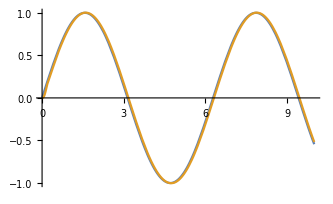

```mathematica
ControlP=TransferFunctionModel[1,s];
n=SystemsModelSeriesConnect[ControlP,Motor];
n=SystemsModelFeedbackConnect[n];
a=OutputResponse[n,Sin[t],{t,0,10}];
Plot[{Sin[t],a},{t,0,10}]
```

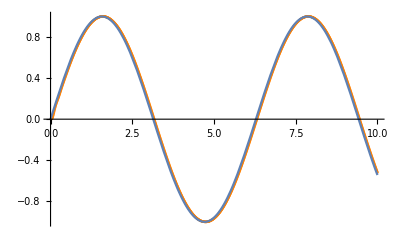

```mathematica
nd=ToDiscreteTimeModel[n,τ];
ad=OutputResponse[nd,Table[Sin[i],{i,0,100,0.01}]]//Flatten;
Show[{ListPlot[Table[{0.01i,ad[[i]]},{i,1000}],PlotStyle->Orange],Plot[Sin[t],{t,0,10}]}]
```

Part::take: Cannot take positions 1 through 2 in ColoresTema.

Part::partd: Part specification ColoresTema⟦3⟧ is longer than depth of object.

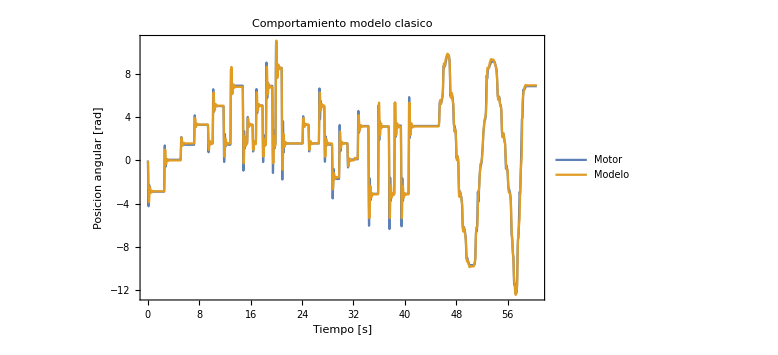
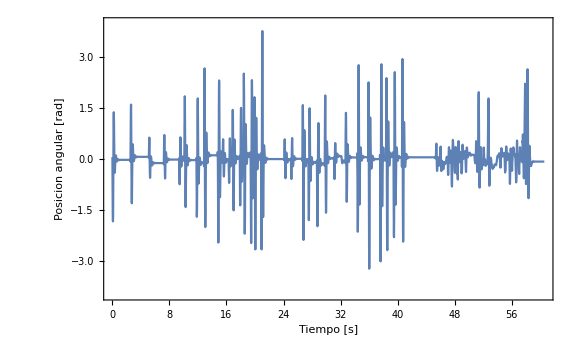
-Graphics-
-Graphics-
Error Absoluto Maximo: 3.76758
Error Absoluto Promedio: 0.0816399
Desviacion Estandar: 0.462756
Error Relativo Maximo: 70.6824
Error Relativo Promedio: 0.0216019
FPE: 0.139435

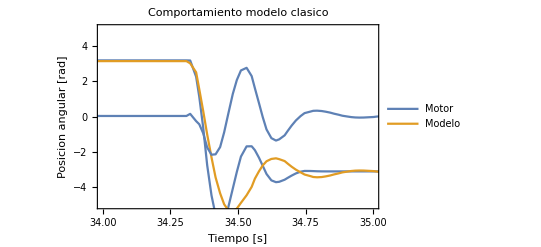

```mathematica
csdo=OutputResponse[nd,SeñalControl[[;;,2]]]//Flatten;
Error=Table[{RespuestaMotor[[i,1]],RespuestaMotor[[i,2]]-csdo[[i]]},{i,1,3821}];
ErrorRelativo=Table[Abs[RespuestaMotor[[i,2]]-csdo[[i]]]/RespuestaMotor[[i,2]],{i,1,3821}];
dm=8;
JFPE=(1+dm/3821)/(1-dm/3821)Sum[1/2 Error[[i,2]]^2,{i,3821}] 1/3821;

CompG=ListLinePlot[{RespuestaMotor,Table[{RespuestaMotor[[i,1]],csdo[[i]]},{i,1,3821}]},
FrameLabel->{"Tiempo [s]","Posicion angular [rad]"},
PlotStyle->ColoresTema[[1;;2]],
PlotLegends->{"Motor","Modelo"},
PlotLabel->Style["Comportamiento modelo clasico",FontSize->20],
Frame->True,
PlotRange->All
];

ErrorG=ListLinePlot[Error,
PlotStyle->ColoresTema[[3]],
PlotLegends->"Error",
PlotRange->{-4,4},
FrameLabel->{"Tiempo [s]","Posicion angular [rad]"},
Frame->True];

GCM=Column[{
Show[CompG,ImagePadding->40,ImageSize->Large],
Show[ErrorG,ImagePadding->40,ImageSize->Large],
Style["Error Absoluto Maximo: "<>ToString[Max[Abs[Error[[;;,2]]]]]<>"
Error Absoluto Promedio: "<>ToString[Median[Abs[Error[[;;,2]]]]]<>"
Desviacion Estandar: "<>ToString[StandardDeviation[Abs[Error[[;;,2]]]]]<>"
Error Relativo Maximo: "<>ToString[Max[Abs[ErrorRelativo]]]<>"
Error Relativo Promedio: "<>ToString[Median[Abs[ErrorRelativo]]]<>"
FPE: "<>ToString[JFPE],TextAlignment->Left]},
Alignment->{Left,Right,Automatic}
]
Show[CompG,ErrorG,PlotRange->{{34,35},{-5,5}}]
Export["ComportamientoModeloClasico.jpg",GCM];
```

## Validación

```mathematica
Run["dir /b > filename.txt"];
Files=Import["filename.txt","List"];
GenVsFPE={{"Genoma","FPE"}};
```

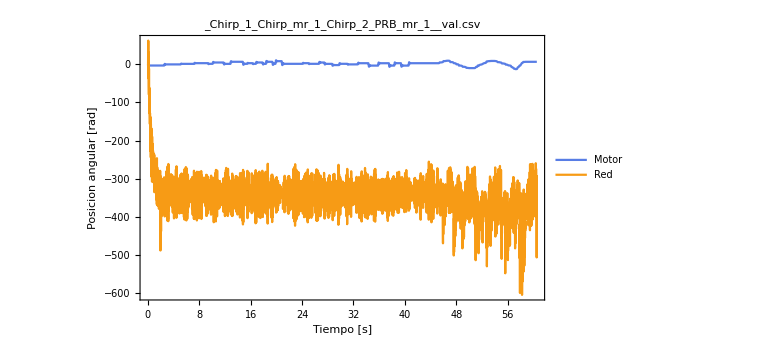
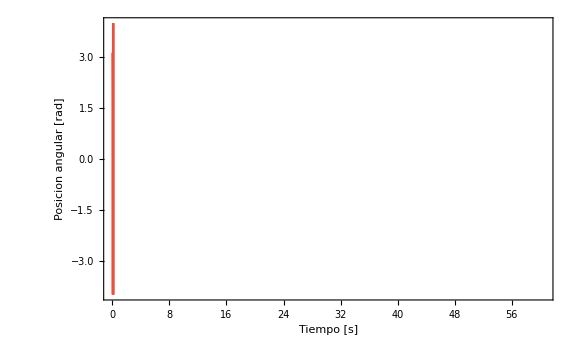
-Graphics-
-Graphics-
Error Absoluto Maximo: 609.608
Error Absoluto Promedio: 338.038
Desviacion Estandar: 47.84
Error Relativo Maximo: 49321.7
Error Relativo Promedio: 107.493
FPE: 61288.7

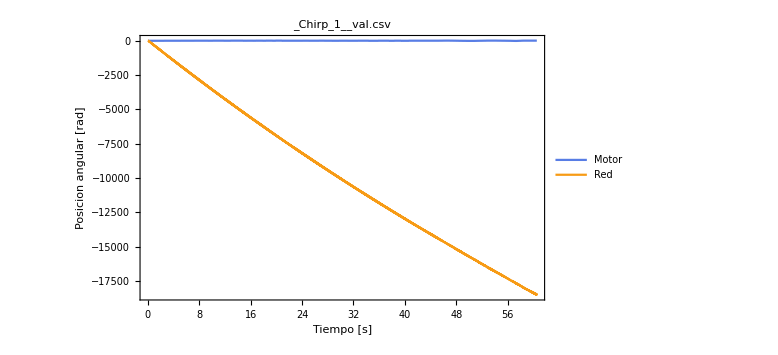
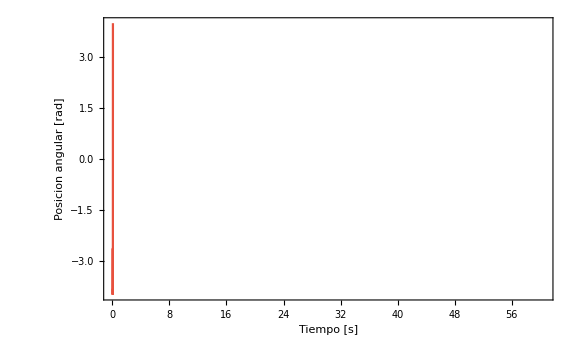
-Graphics-
-Graphics-
Error Absoluto Maximo: 18521.7
Error Absoluto Promedio: 10017.3
Desviacion Estandar: 5295.92
Error Relativo Maximo:           6
1.35078 10
Error Relativo Promedio: 3461.82
FPE:           7
6.19852 10

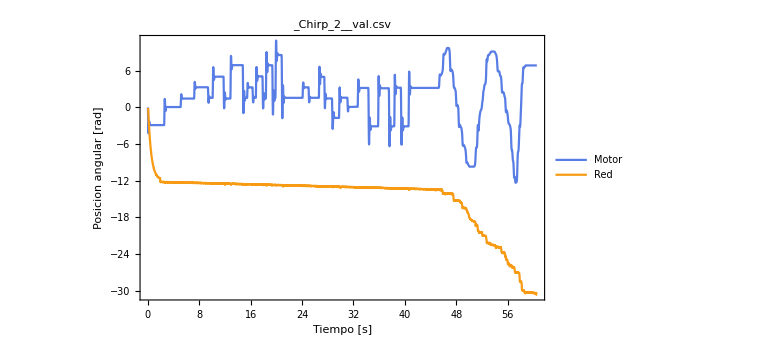
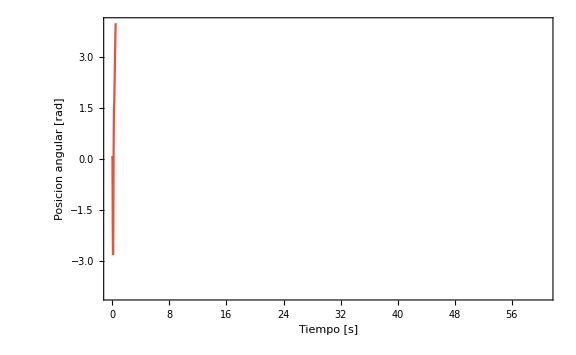
-Graphics-
-Graphics-
Error Absoluto Maximo: 37.5286
Error Absoluto Promedio: 15.6626
Desviacion Estandar: 6.32054
Error Relativo Maximo: 1691.81
Error Relativo Promedio: 5.18504
FPE: 159.283

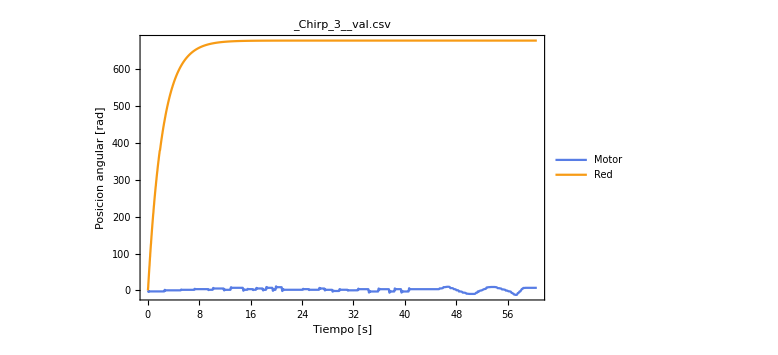
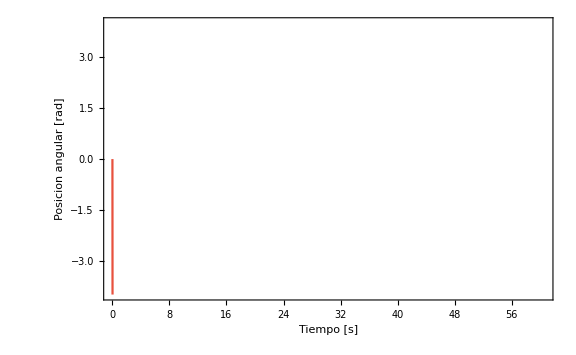
-Graphics-
-Graphics-
Error Absoluto Maximo: 690.772
Error Absoluto Promedio: 675.311
Desviacion Estandar: 88.6368
Error Relativo Maximo: 88463.4
Error Relativo Promedio: 211.855
FPE: 217225.

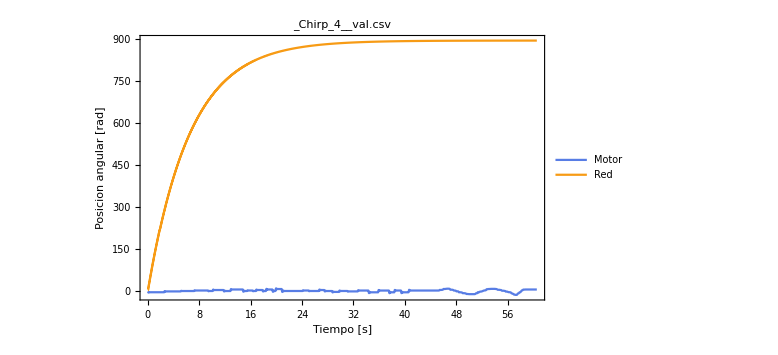
-Graphics-
-Graphics-
Error Absoluto Maximo: 906.119
Error Absoluto Promedio: 883.811
Desviacion Estandar: 183.758
Error Relativo Maximo: 115540.
Error Relativo Promedio: 278.988
FPE: 334108.

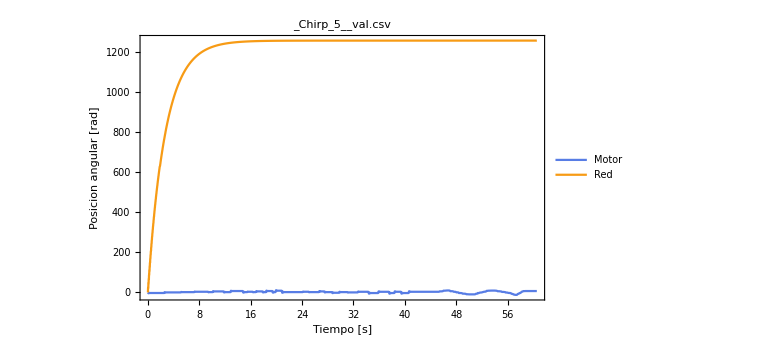
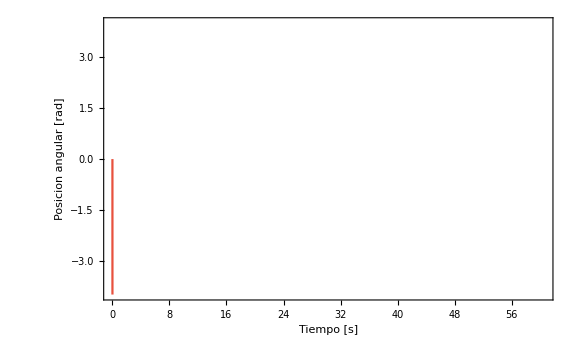
-Graphics-
-Graphics-
Error Absoluto Maximo: 1269.04
Error Absoluto Promedio: 1253.39
Desviacion Estandar: 177.571
Error Relativo Maximo: 163836.
Error Relativo Promedio: 393.222
FPE: 741323.

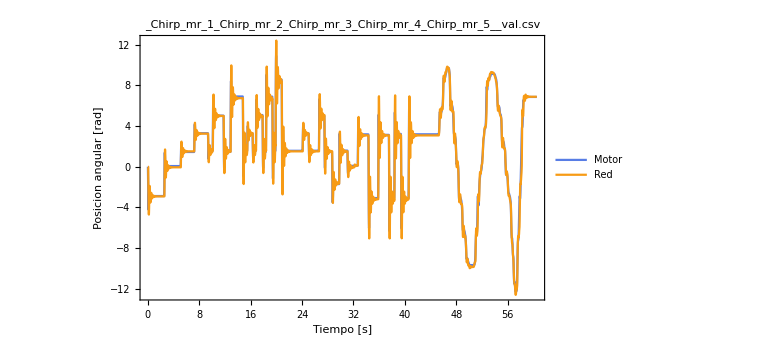
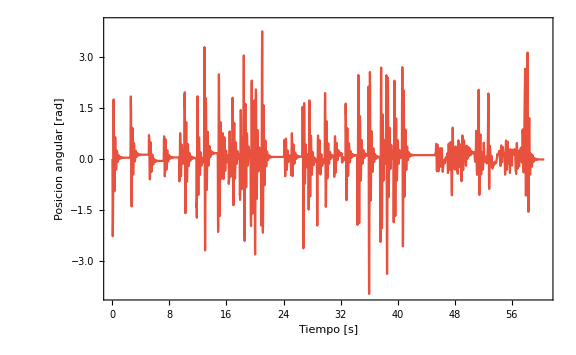
-Graphics-
-Graphics-
Error Absoluto Maximo: 3.98154
Error Absoluto Promedio: 0.126692
Desviacion Estandar: 0.50282
Error Relativo Maximo: 69.0146
Error Relativo Promedio: 0.0421141
FPE: 0.18249

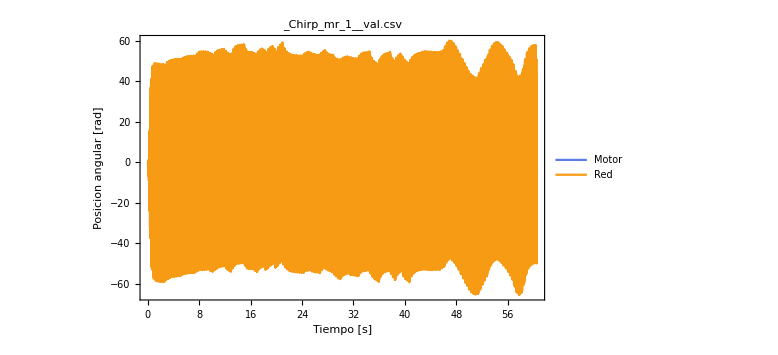
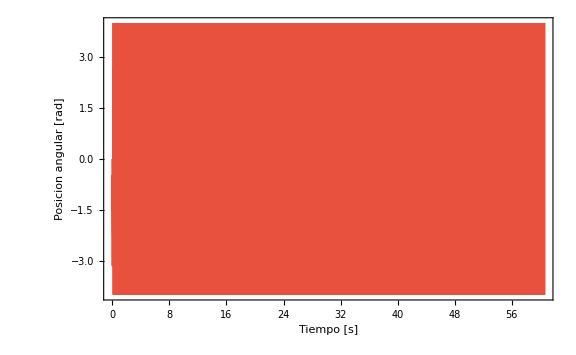
-Graphics-
-Graphics-
Error Absoluto Maximo: 68.0623
Error Absoluto Promedio: 43.8034
Desviacion Estandar: 17.6789
Error Relativo Maximo: 6674.22
Error Relativo Promedio: 11.8235
FPE: 855.286

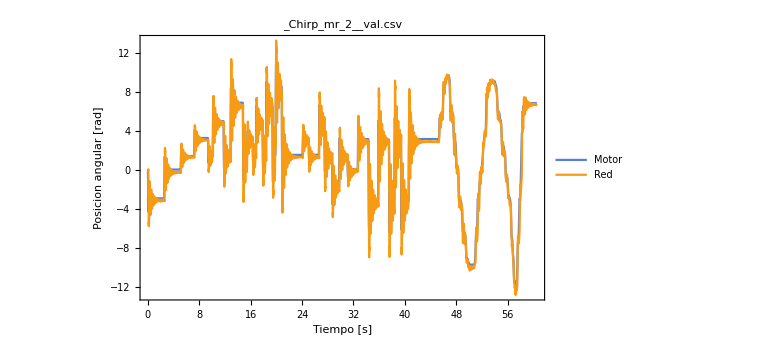
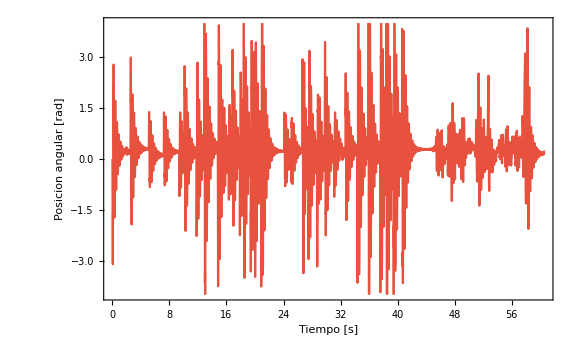
-Graphics-
-Graphics-
Error Absoluto Maximo: 5.60088
Error Absoluto Promedio: 0.371633
Desviacion Estandar: 0.783724
Error Relativo Maximo: 62.0579
Error Relativo Promedio: 0.137107
FPE: 0.544928

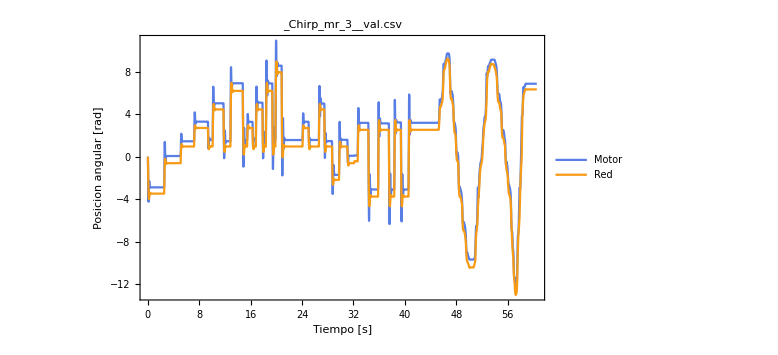
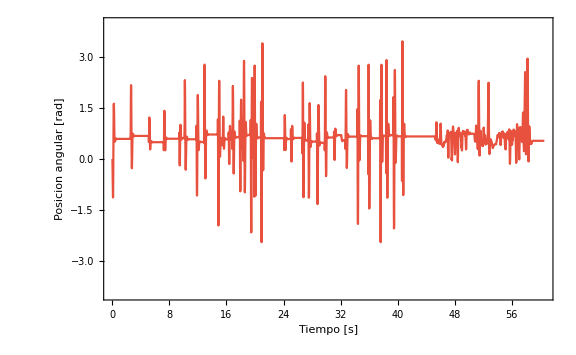
-Graphics-
-Graphics-
Error Absoluto Maximo: 3.46427
Error Absoluto Promedio: 0.617127
Desviacion Estandar: 0.351719
Error Relativo Maximo: 29.2982
Error Relativo Promedio: 0.207268
FPE: 0.291813

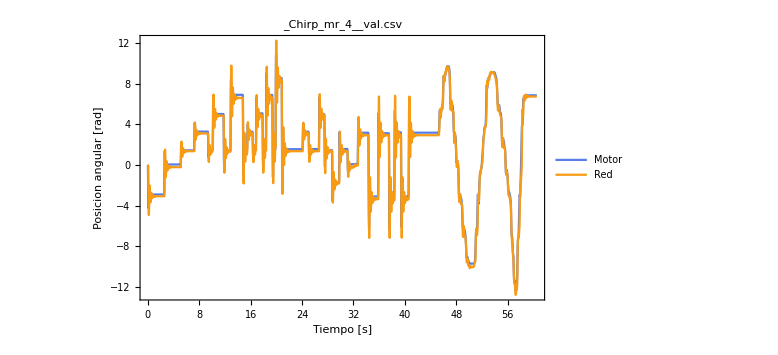
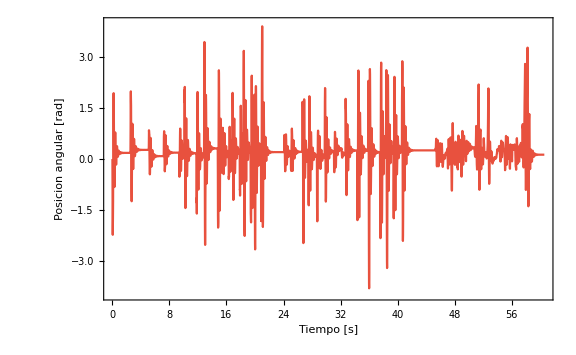
-Graphics-
-Graphics-
Error Absoluto Maximo: 3.90759
Error Absoluto Promedio: 0.249852
Desviacion Estandar: 0.486856
Error Relativo Maximo: 51.4218
Error Relativo Promedio: 0.0785037
FPE: 0.198516

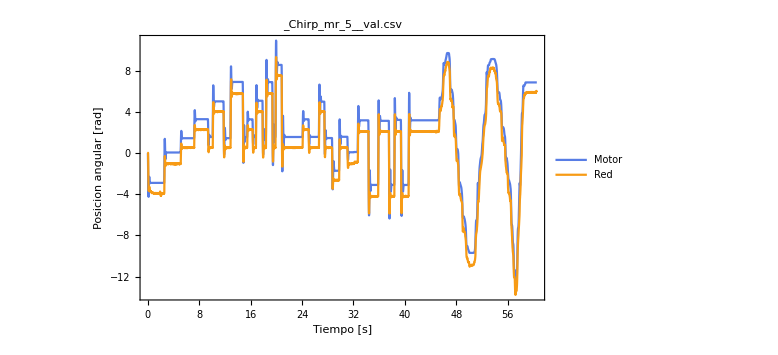
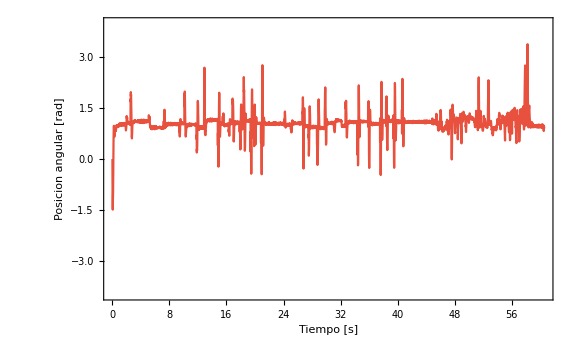
-Graphics-
-Graphics-
Error Absoluto Maximo: 3.37898
Error Absoluto Promedio: 1.05187
Desviacion Estandar: 0.255681
Error Relativo Maximo: 116.499
Error Relativo Promedio: 0.343296
FPE: 0.600232

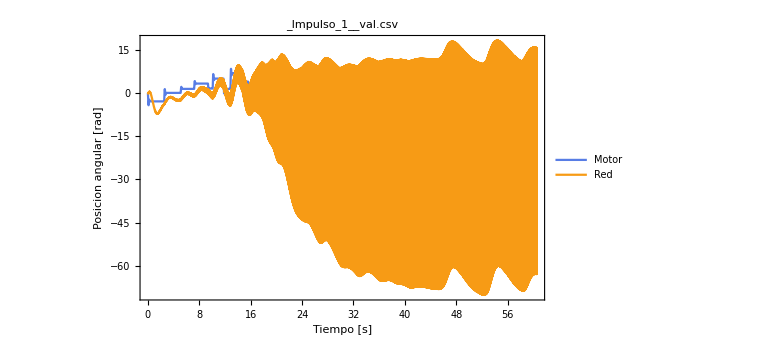
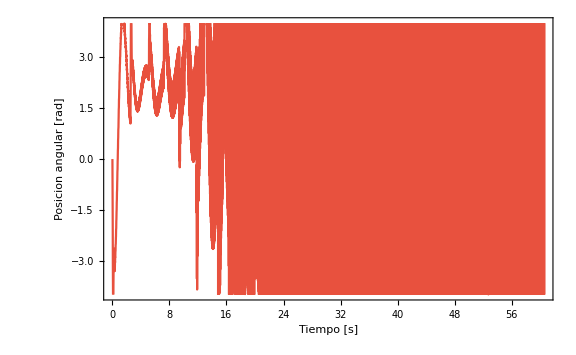
-Graphics-
-Graphics-
Error Absoluto Maximo: 77.4175
Error Absoluto Promedio: 9.65812
Desviacion Estandar: 26.4959
Error Relativo Maximo: 7880.32
Error Relativo Promedio: 4.58461
FPE: 682.385

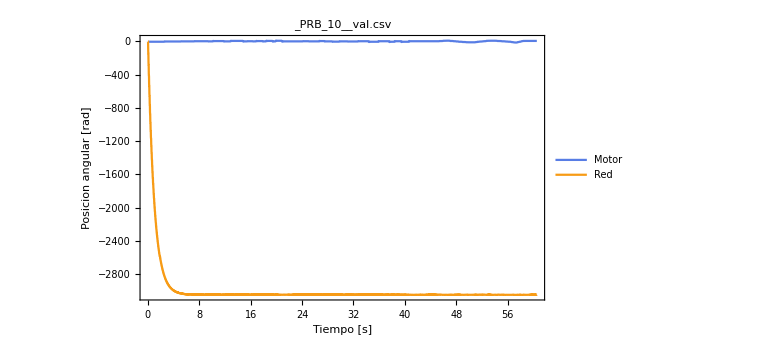
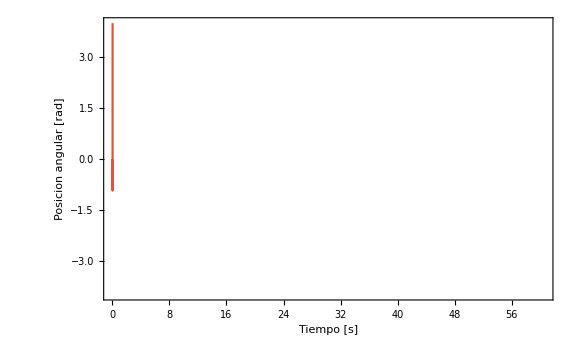
-Graphics-
-Graphics-
Error Absoluto Maximo: 3058.74
Error Absoluto Promedio: 3049.39
Desviacion Estandar: 273.923
Error Relativo Maximo: 397376.
Error Relativo Promedio: 957.02
FPE:          6
4.5635 10

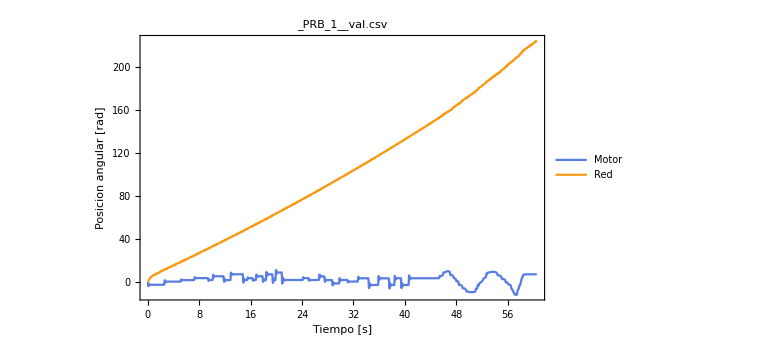
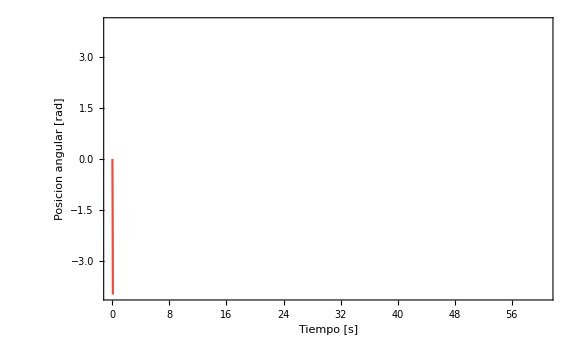
-Graphics-
-Graphics-
Error Absoluto Maximo: 221.235
Error Absoluto Promedio: 96.3697
Desviacion Estandar: 62.426
Error Relativo Maximo: 13130.2
Error Relativo Promedio: 33.0234
FPE: 6981.

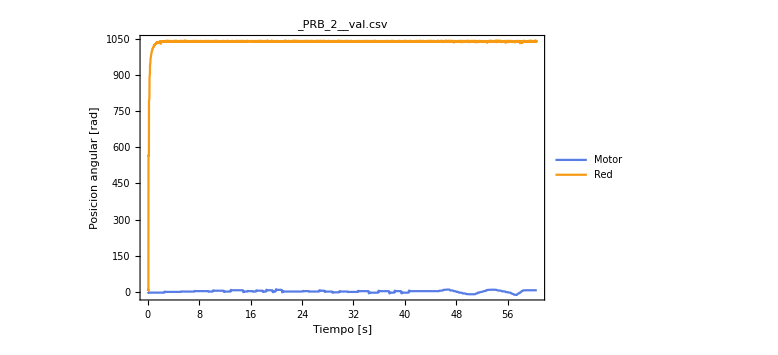
-Graphics-
-Graphics-
Error Absoluto Maximo: 1053.75
Error Absoluto Promedio: 1037.78
Desviacion Estandar: 42.4572
Error Relativo Maximo: 135616.
Error Relativo Promedio: 325.86
FPE: 546701.

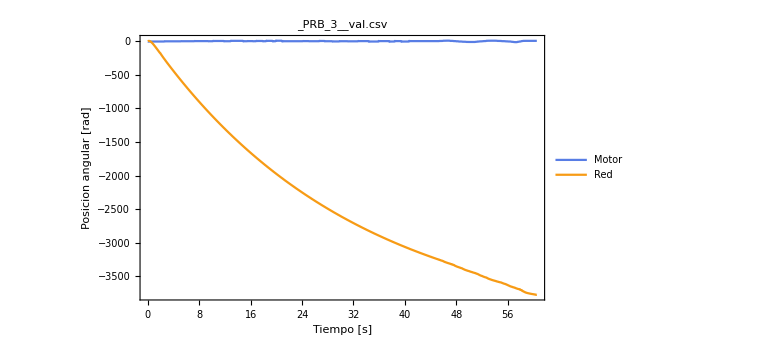
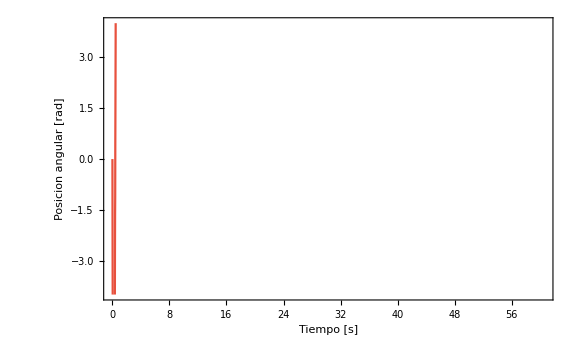
-Graphics-
-Graphics-
Error Absoluto Maximo: 3782.89
Error Absoluto Promedio: 2599.91
Desviacion Estandar: 1057.48
Error Relativo Maximo: 347018.
Error Relativo Promedio: 880.701
FPE:           6
3.36721 10

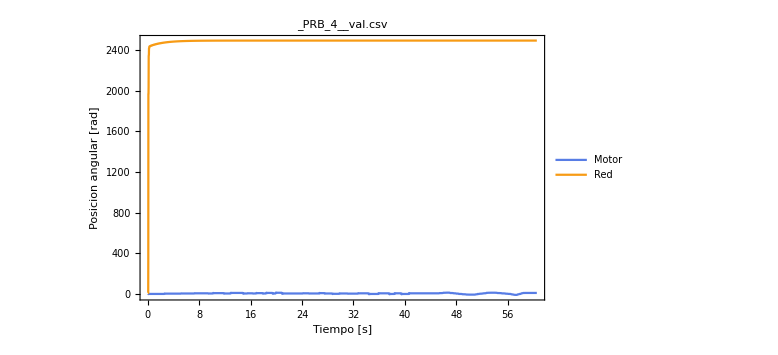
-Graphics-
-Graphics-
Error Absoluto Maximo: 2507.4
Error Absoluto Promedio: 2491.9
Desviacion Estandar: 79.3919
Error Relativo Maximo: 325309.
Error Relativo Promedio: 782.876
FPE:           6
3.13771 10

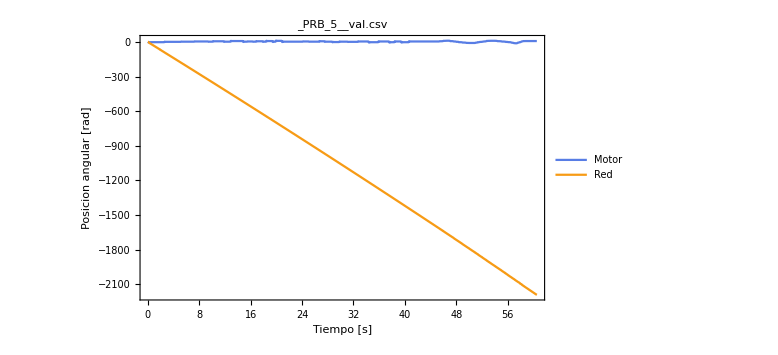
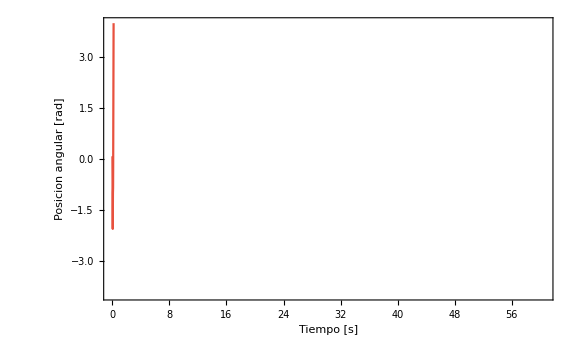
-Graphics-
-Graphics-
Error Absoluto Maximo: 2197.08
Error Absoluto Promedio: 1055.54
Desviacion Estandar: 626.115
Error Relativo Maximo: 143009.
Error Relativo Promedio: 370.048
FPE: 767351.

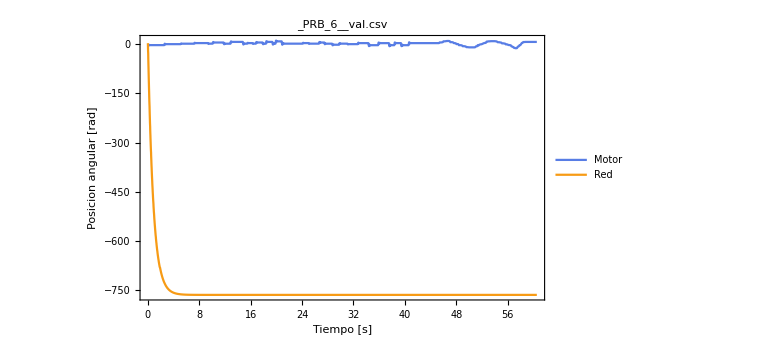
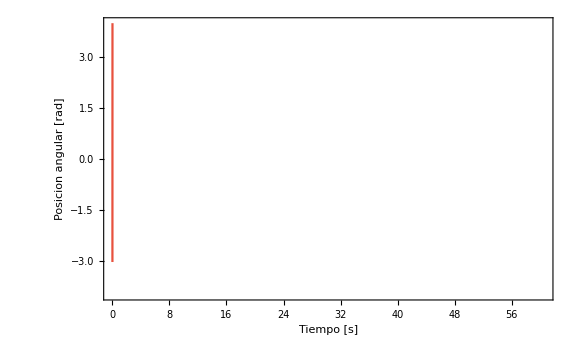
-Graphics-
-Graphics-
Error Absoluto Maximo: 775.48
Error Absoluto Promedio: 766.249
Desviacion Estandar: 64.1838
Error Relativo Maximo: 99680.9
Error Relativo Promedio: 240.851
FPE: 288609.

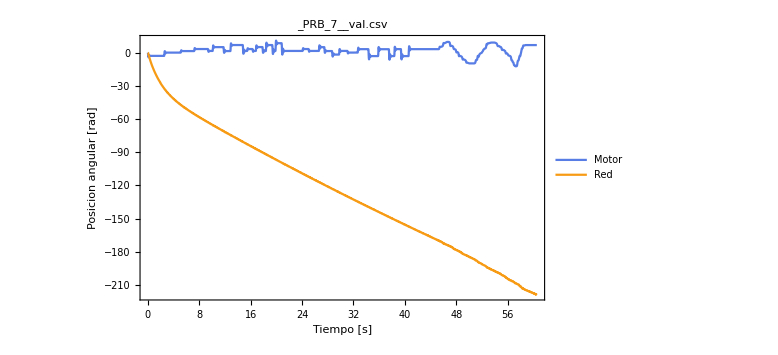
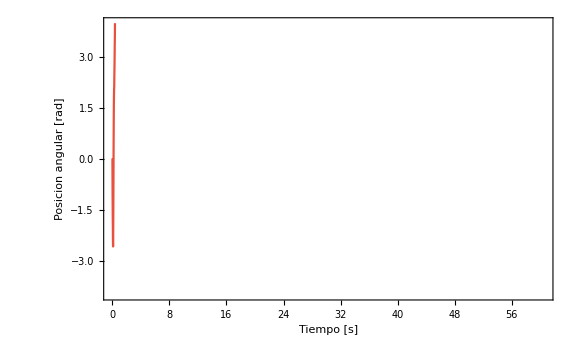
-Graphics-
-Graphics-
Error Absoluto Maximo: 225.822
Error Absoluto Promedio: 128.331
Desviacion Estandar: 54.2695
Error Relativo Maximo: 16967.3
Error Relativo Promedio: 44.6024
FPE: 9589.35

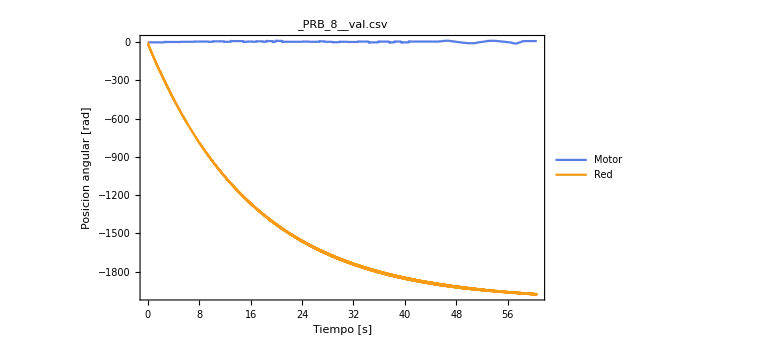
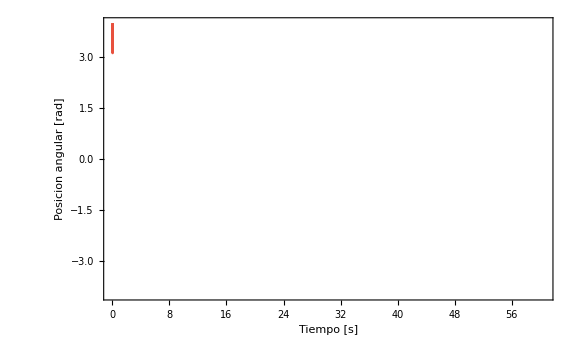
-Graphics-
-Graphics-
Error Absoluto Maximo: 1989.85
Error Absoluto Promedio: 1702.9
Desviacion Estandar: 516.658
Error Relativo Maximo: 224392.
Error Relativo Promedio: 558.584
FPE:           6
1.26849 10

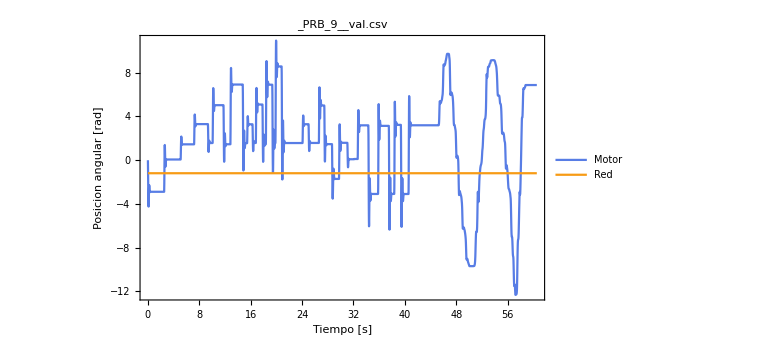
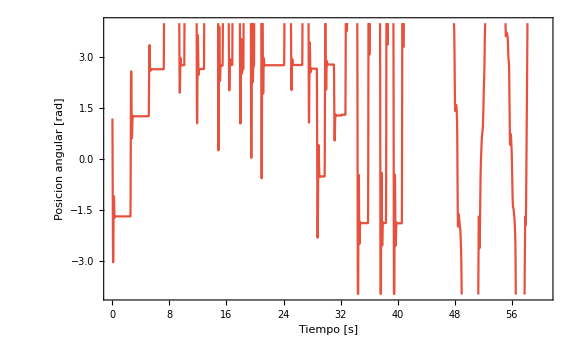
-Graphics-
-Graphics-
Error Absoluto Maximo: 12.1251
Error Absoluto Promedio: 4.32941
Desviacion Estandar: 2.66016
Error Relativo Maximo: 193.834
Error Relativo Promedio: 1.36282
FPE: 13.0137

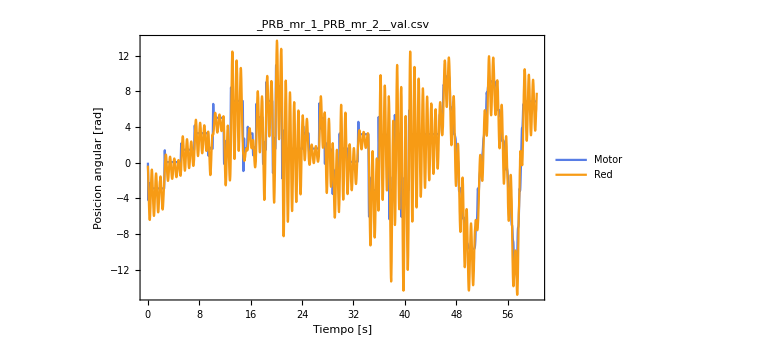
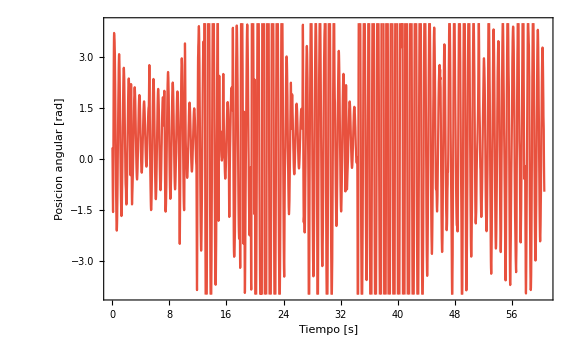
-Graphics-
-Graphics-
Error Absoluto Maximo: 13.6658
Error Absoluto Promedio: 1.95223
Desviacion Estandar: 2.06745
Error Relativo Maximo: 443.478
Error Relativo Promedio: 0.631138
FPE: 5.29552

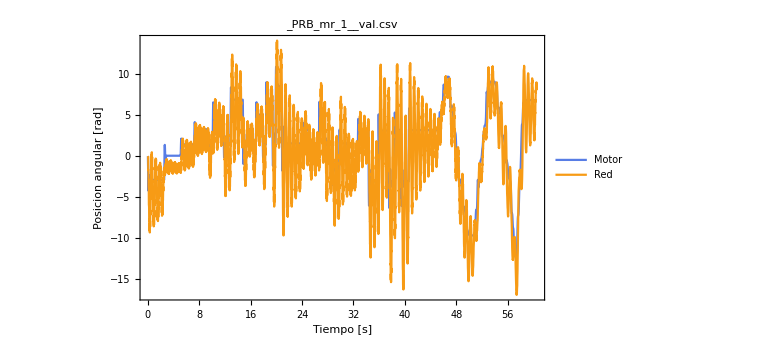
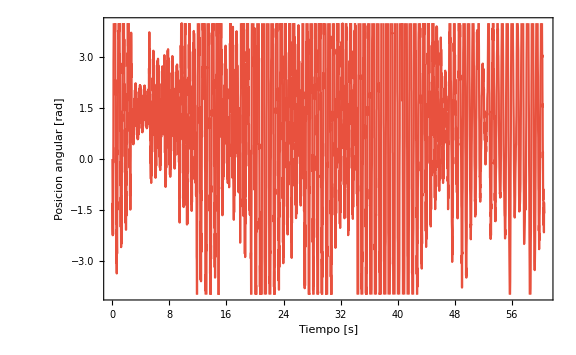
-Graphics-
-Graphics-
Error Absoluto Maximo: 15.1772
Error Absoluto Promedio: 2.29779
Desviacion Estandar: 2.29191
Error Relativo Maximo: 266.498
Error Relativo Promedio: 0.741407
FPE: 6.70729

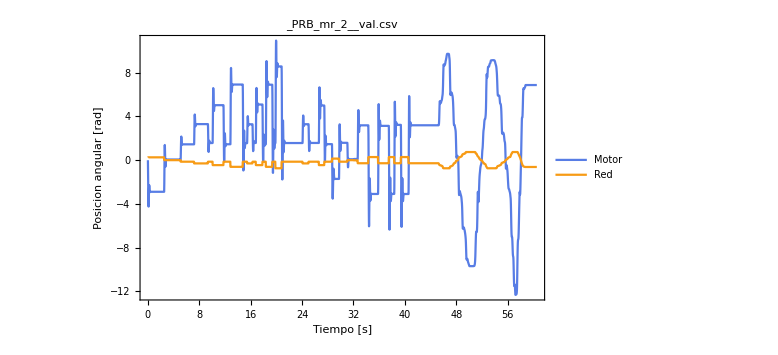
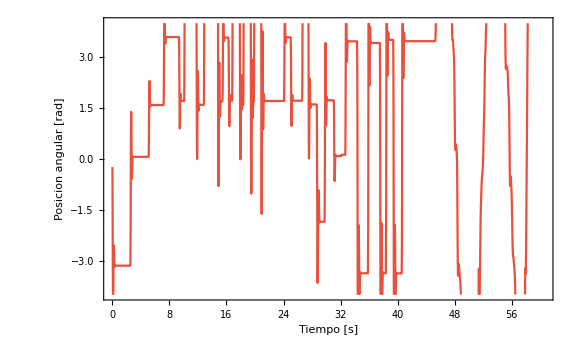
-Graphics-
-Graphics-
Error Absoluto Maximo: 13.0585
Error Absoluto Promedio: 3.46536
Desviacion Estandar: 2.82971
Error Relativo Maximo: 39.4677
Error Relativo Promedio: 1.08909
FPE: 11.9239

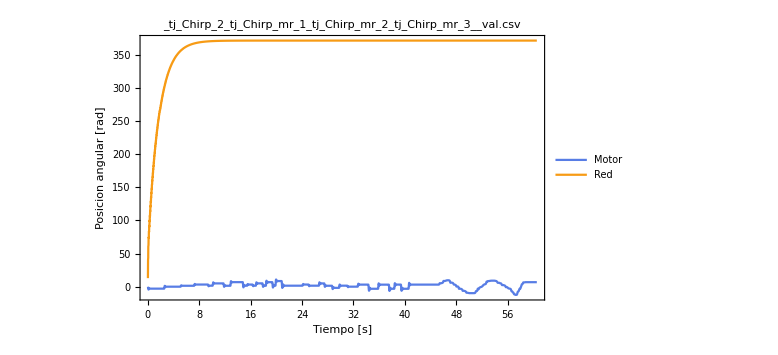
-Graphics-
-Graphics-
Error Absoluto Maximo: 383.83
Error Absoluto Promedio: 368.326
Desviacion Estandar: 35.9888
Error Relativo Maximo: 48438.9
Error Relativo Promedio: 115.549
FPE: 66256.2

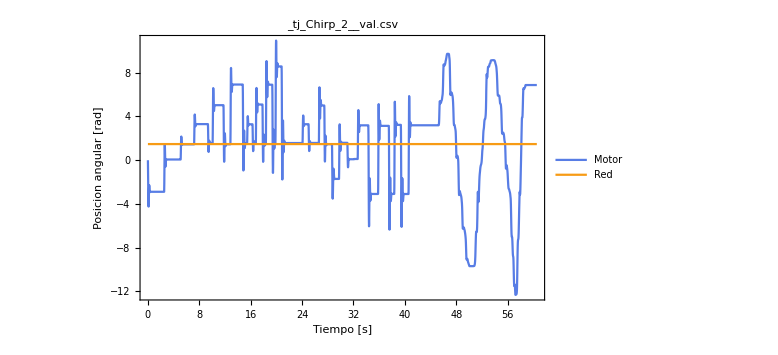
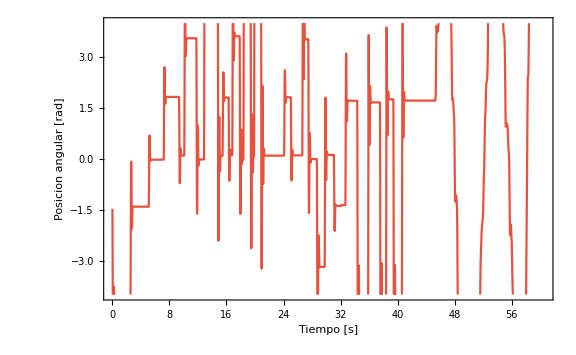
-Graphics-
-Graphics-
Error Absoluto Maximo: 13.7859
Error Absoluto Promedio: 1.82547
Desviacion Estandar: 2.77885
Error Relativo Maximo: 240.495
Error Relativo Promedio: 0.707577
FPE: 8.57801

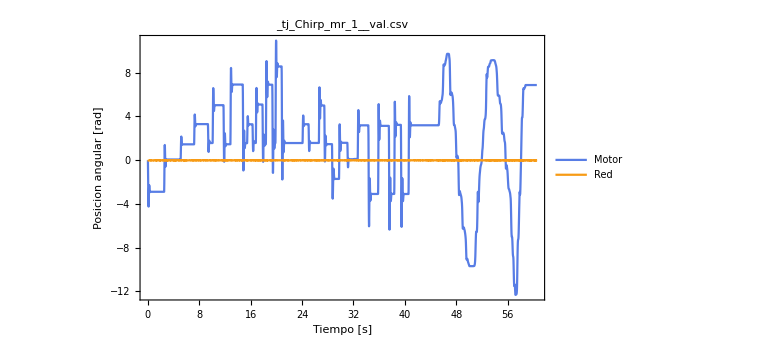
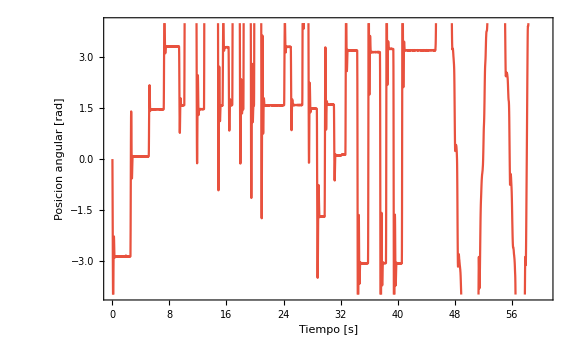
-Graphics-
-Graphics-
Error Absoluto Maximo: 12.3033
Error Absoluto Promedio: 3.19642
Desviacion Estandar: 2.61803
Error Relativo Maximo: 1.707
Error Relativo Promedio: 1.00398
FPE: 10.1713

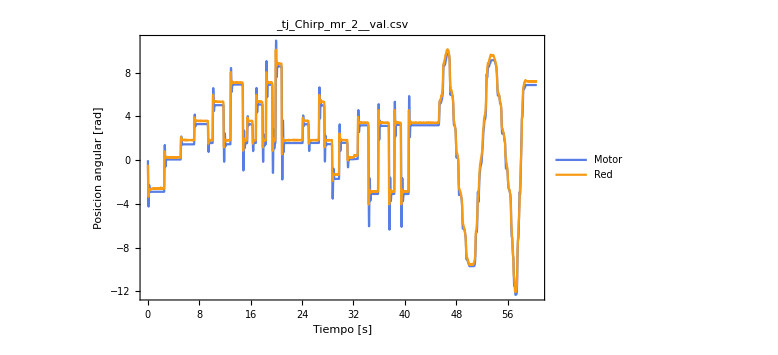
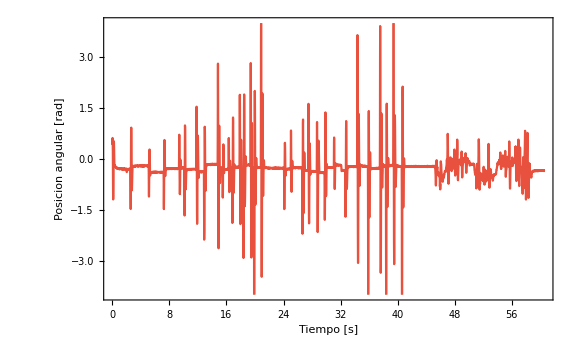
-Graphics-
-Graphics-
Error Absoluto Maximo: 5.39298
Error Absoluto Promedio: 0.273057
Desviacion Estandar: 0.439453
Error Relativo Maximo: 67.3909
Error Relativo Promedio: 0.0883417
FPE: 0.174128

```mathematica
For[j=1,j<=Length[Files],j++,
If[StringCount[Files[[j]],".csv"]>0&&!(Files[[j]]=="ControlSignal.csv"||Files[[j]]=="MotorReactionToControlP.csv"||Files[[j]]=="ValidationControlnMotorReaction.csv") ,



csdo=Import[Files[[j]],"Data"][[;;,2]];


Error=Table[{RespuestaMotor[[i,1]],RespuestaMotor[[i,2]]-csdo[[i]]},{i,1,3821}];
ErrorRelativo=Table[Abs[RespuestaMotor[[i,2]]-csdo[[i]]]/RespuestaMotor[[i,2]],{i,1,3821}];
dm=Complejidad[[
Evaluate[
Position[Complejidad,
StringReplace[Files[[j]],"_val.csv"->""]][[1,1]]]
,2
]];
JFPE=(1+(dm/3821))/(1-(dm/3821))Sum[1/2 Error[[i,2]]^2,{i,3821}] 1/3821;
GenVsFPE=Join[GenVsFPE,{{Files[[j]],JFPE}}];

CompG=ListLinePlot[{RespuestaMotor,Table[{RespuestaMotor[[i,1]],csdo[[i]]},{i,1,3821}]},
FrameLabel->{"Tiempo [s]","Posicion angular [rad]"},
PlotLegends->{"Motor","Red"},
PlotStyle->ColoresTema[[1;;2]],
PlotLabel->Style[Files[[j]],FontSize->12],
Frame->True,
PlotRange->Full
];

ErrorG=ListLinePlot[Error,
PlotStyle->ColoresTema[[3]],
PlotLegends->"Error",
PlotRange->{-4,4},
FrameLabel->{"Tiempo [s]","Posicion angular [rad]"},
Frame->True];

GCM=Column[{
Show[CompG,ImagePadding->60,ImageSize->Large],
Show[ErrorG,ImagePadding->60,ImageSize->Large],
Style["Error Absoluto Maximo: "<>ToString[Max[Abs[Error[[;;,2]]]]]<>"
Error Absoluto Promedio: "<>ToString[Median[Abs[Error[[;;,2]]]]]<>"
Desviacion Estandar: "<>ToString[StandardDeviation[Abs[Error[[;;,2]]]]]<>"
Error Relativo Maximo: "<>ToString[Max[Abs[ErrorRelativo]]]<>"
Error Relativo Promedio: "<>ToString[Median[Abs[ErrorRelativo]]]<>"
FPE: "<>ToString[JFPE],TextAlignment->Left]},
Alignment->{Left,Right,Automatic}
];
Export[StringReplace[Files[[j]],".csv"-> ""]<>".jpg",GCM];
Print[GCM]
];
]
```

## Pruebas